```mathematica
b=0.5;
Integrate[-p DiracDelta[(x-b)],{x,0,1}]
```

-p

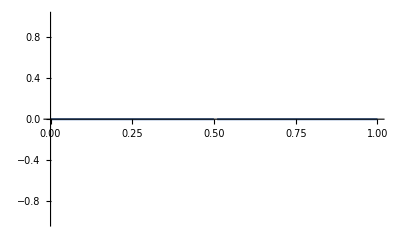

```mathematica
Plot[2DiracDelta[(x-b)],{x,0,1},PlotRange->All]
```

```mathematica
Clear[b,y]
y[x_]:=a x^2 +b x+c
eq1=y[0]==0
eq2=y[6]==3
eq3=y[9]==0
Solve[{eq1,eq2,eq3},{a,b,c}]
```

c==0

36 a+6 b+c==3

81 a+9 b+c==0

{{a→-1/6,b→3/2,c→0}}

```mathematica
pc=-Piecewise[{{21.15 x-2x^2,x<=3},{21.25x-2 x^2 -10(x-3),3<=x<=6},{12.75 (8-x),6<=x<=8}}]
```

-(Piecewise[{{21.15 x-2 x^2, x≤3}, {-10 (-3+x)+21.25 x-2 x^2, 3≤x≤6}, {12.75 (8-x), 6≤x≤8}, {0, True}}])

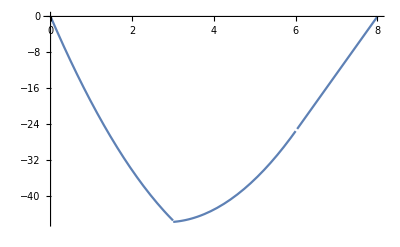

```mathematica
Plot[pc,{x,0,8}]
```

```mathematica
y[1]
```

a+c

```mathematica
(8./Sqrt[68])^2
```

```mathematica
0.9411764705882353 8.5
```

8.

```mathematica
y[x_]:=8.5 0.9411(a x^2 +b x+c)-(21.25-2x^2)
eq1=y[0]==0
eq2=y[6]==3
eq3=y[8]==0
sol=Solve[{eq1,eq2,eq3},{a,b,c}]
y[x]/.sol[[1]]//Simplify
```

-21.25+7.99935 c==0

50.75+7.99935 (36 a+6 b+c)==3

106.75+7.99935 (64 a+8 b+c)==0

{{a→-0.281273,b→0.25002,c→2.65647}}

3.55271×10^-15+2. x-0.25 x^2

3.55271×10^-15+2. x-0.25 x^2

```mathematica
y[x_]:=8.5 0.9411(a x^2 +b x+c)-(21.25 x-2 x^2-10(8-x))
eq1=y[0]==0
eq2=y[6]==3
eq3=y[8]==0
sol=Solve[{eq1,eq2,eq3},{a,b,c}]
y[x]/.sol[[1]]//Simplify
```

80.+7.99935 c==0

-35.5+7.99935 (36 a+6 b+c)==3

-42.+7.99935 (64 a+8 b+c)==0

{{a→-0.281273,b→4.15659,c→-10.0008}}

-1.42109×10^-14+2. x-0.25 x^2

```mathematica
y[x_]:=8.5 (a x^2 +b x+c)-(12.75(8-x))
eq1=y[0]==0
eq2=y[6]==3
eq3=y[8]==0
sol=Solve[{eq1,eq2,eq3},{a,b,c}]
y[x]/.sol[[1]]//Simplify
```

-102.+8.5 c==0

-25.5+8.5 (36 a+6 b+c)==3

0.+8.5 (64 a+8 b+c)==0

{{a→-0.0294118,b→-1.26471,c→12.}}

0.+2. x-0.25 x^2

```mathematica
ArcTan[1.25]
```

0.896055

```mathematica
5/Sqrt[5 5+4 4.]
```

0.780869

```mathematica
5/0.6246
```

8.00512

```mathematica
25/4.
```

6.25

```mathematica
5/0.624
```

8.01282

```mathematica
73/8.
```

9.125

```mathematica
17-9.125
```

7.875

```mathematica
3.875/0.6
```

6.45833

```mathematica
-7.875 4+4 4
```

```mathematica
-15.5/3
```

-5.16667

```mathematica
9.125 4
```

36.5

```mathematica
-3/0.8
```

-3.75

```mathematica
5.167/0.8
```

6.45875

```mathematica
-3 3+9.125 4
```

```mathematica
27.5/4
```

6.875

```mathematica
6.458 0.6
```

3.8748

```mathematica
(-2 4 12-2 4 8-3 3)/4.
```

-42.25

```mathematica
16-42.25
```

-26.25

```mathematica
26.25/0.6
```

43.75

```mathematica
26.25 4
```

105.

```mathematica
105-9
```

96

```mathematica
96/3.
```

32.

```mathematica
26.25 4
```

105.

```mathematica
105-9
```

96

```mathematica
96/3.
```

32.

```mathematica
(42.25-26.25)
```

16.

```mathematica
26.25 8
```

210.

```mathematica
42.25 4
```

169.

```mathematica
169-210+9
```

-32

```mathematica
32/3.
```

10.6667

```mathematica
8/0.6
```

13.3333

```mathematica
(42.25-26.25)/0.6
```

26.6667

```mathematica
-2 4 12
```

-96

```mathematica
2 4 8
```

64

```mathematica
(-2 4 12-2 4 8-3 3)
```

-169

```mathematica
Clear[y]
Integrate[x/y + y/x,{x,-1,1},{y,-1,1}]
```

0

```mathematica
Log[0]
```

-∞

```mathematica
4/Sqrt[20.]
```

0.894427

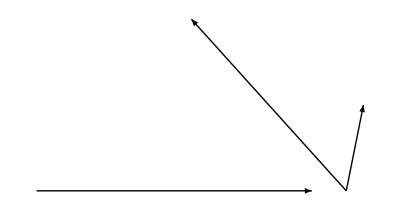

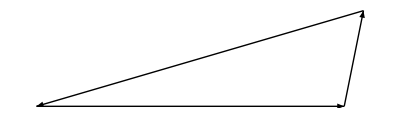

```mathematica
p1={0.9,0};
p2={1,0.5};
p3={0.7,0};
p4={0,1};
Graphics[Arrow[{{p1,p2},{-p1,p3},{p1,p4}}]]
Graphics[Arrow[{{p2,-p3},{-p3,p1},{p1,p2}}]]
```

```mathematica
{0,-1}+{-1,0}
```

{-1,-1}

```mathematica
(p3-p1)+(p2-p3)
```

{0.1,0.5}

```mathematica
p2-p1
```

{0.1,0.5}

```mathematica
Integrate[(-q x x/2)+q L x/2 ,x,x]//Expand
```

```mathematica
Solve[1/12 L q L^3-(q L^4)/24+C1 L==0,C1]//Simplify
```

{{C1→-(L^3 q)/24}}

```mathematica
Integrate[(L-X)(PP/2)(X-L)^2 /(ei),{X,0,L}]//Simplify
```

(L^4 PP)/(8 ei)

```mathematica
1/(ei)Integrate[-PP x x/2 + PP L x-PP (L^2)/2,x,x]/.x->L
```

-(L^4 PP)/(8 ei)

```mathematica
Integrate[(PP (L^2 x+L x^2-x^3/3))/(2 ei)+L PP x+,x]
```

```mathematica
v=PP L x+(L^2 PP x^2)/(4 ei)+(L PP x^3)/(6 ei)-(PP x^4)/(24 ei)+(L^2 PP)/2
```

(L^2 PP)/2+L PP x+(L^2 PP x^2)/(4 ei)+(L PP x^3)/(6 ei)-(PP x^4)/(24 ei)

```mathematica
v/.x->L//Simplify
```

(3 L^2 (4 ei+L^2) PP)/(8 ei)

```mathematica
48/7
```

48/7

```mathematica
729.6/(2.05 10^8 8 10^-6)
```

0.444878

```mathematica
L=5;
q=5;
Integrate[0.8 x (-q x x/2+q L x/2),{x,5,0}]/(2.05 10^8 8.333 10^-6)
```

-0.060978

```mathematica
Clear[L,q]
Integrate[0.8 x (-q x x/2+q L x/2),x]
```

-0.4 q (-0.333333 L x^3+0.25 x^4)

```mathematica
40 4+40 2
```

240

```mathematica
240/6
```

40

```mathematica
40 6
```

240

```mathematica
10 4 4/8
```

20

```mathematica
y[x_]=a x^2+b x+c
Solve[{y[0]==0,y[2]==140,y[4]==240},{a,b,c}]
```

c+b x+a x^2

{{a→-5,b→80,c→0}}

```mathematica
y[x_]=a x+b
Solve[{y[0]==240,y[6]==0},{a,b}]
```

b+a x

{{a→-40,b→240}}

```mathematica
Solve[(PP L^2)/2 ==((c1 x+(L^2 PP x^2)/(4 ei)+(L PP x^3)/(6 ei)-(PP x^4)/(24 ei)+c2)/.x->0),c2]
Solve[PP L ==(D[(c1 x+(L^2 PP x^2)/(4 ei)+(L PP x^3)/(6 ei)-(PP x^4)/(24 ei)+(L^2 PP)/2),x]/.x->0),c1]
```

{{c2→(L^2 PP)/2}}

{{c1→L PP}}

```mathematica
(PP (L^2 x+L x^2-x^3/3))/(2 ei)+c1
```

```mathematica
Integrate[-PP x+PP L,x]//Simplify
```

PP (L x-x^2/2)

```mathematica
e=2.05 10^8;
i=2.058 10^-5;
G=e/(2(1+0.3));
a=0.0126;
m=(Integrate[(-5x^2+80 x)x,{x,0,4}]+Integrate[(240-40 x)(4-(x/6)),{x,0,6}])(1/(e i))
q=(Integrate[80-10 x,{x,0,4}]+Integrate[(-40)(-0.16666666) ,{x,0,6}])(1/(G a))
n=(Integrate[40 0.1666666,{x,0,4}]+Integrate[40 1 ,{x,0,6}]+Integrate[(-40 )(-0.166666) ,{x,0,3}])(1/(e a))
```

0.954435

0.000281843

0.000110982

```mathematica
m+q+n
```

0.954828

```mathematica
240/4
```

60

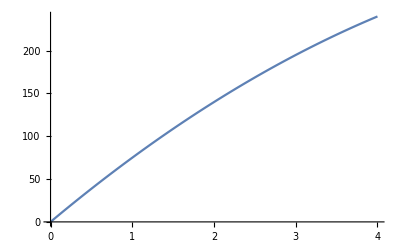

```mathematica
Plot[(-5x^2+80 x),{x,0,4}]
```

```mathematica
e a
```

2.583×10^6

```mathematica
e i
```

4218.9

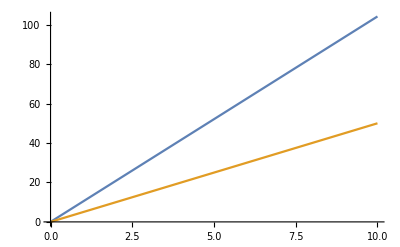

```mathematica
yi[b_,h_]:=b h^3/12
ya[b_,h_]:= b h
Plot[{yi[b,5],ya[b,5]},{b,0,10}]
```

```mathematica
yi[0.1,1]
ya[0.1,1]
```

0.00833333

0.1

```mathematica
-24 3-3 9
```

-99

```mathematica
99/6.
```

16.5

```mathematica
27-16.5
```

10.5

```mathematica
4 36/8.
```

18.

```mathematica
4.5-18
```

-13.5

```mathematica
Clear[a]
y[x_]=a x^2+b x+c
Solve[{y[0]==0,y[3]==13.8,y[6]==-9},{a,b,c}]
```

c+b x+a x^2

{{a→-2.03333,b→10.7,c→0.}}

```mathematica
y[x_]=a x+b
Solve[{y[0]==-9,y[3]==0},{a,b}]
```

b+a x

{{a→3,b→-9}}

```mathematica
(Integrate[(-2.033 x^2 +10.7 x)(x/6),{x,0,6}])/(e i)
```

0.004413

```mathematica
i
```

0.00002058

```mathematica
(0.01 0.02^3)/12
```

6.66667×10^-9

```mathematica
Sqrt[6^2 + 4^2.]
```

```mathematica
6/7.211102550927978
```

0.83205

```mathematica
4/7.2111
```

0.5547

```mathematica
30/4.
```

7.5

```mathematica
10/0.8
```

12.5

```mathematica
12.5 0.6
```

7.5

```mathematica
9/12.
```

0.75

```mathematica
0.75/4
```

0.1875

```mathematica
0.25/0.5547
```

0.450694

```mathematica
0.25 9/4
```

0.5625

```mathematica
0.25/0.8
```

0.3125

```mathematica
0.3125 0.6
```

0.1875

```mathematica
0.75/0.8
```

0.9375

```mathematica
0.9375 0.6
```

0.5625

```mathematica
8
```

```mathematica
0.5547 0.4507
```

0.250003

```mathematica
(
(7.5 0.1875 3)
+((-12.5)(-0.3125) 5)
+((-7.5)(-0.1875) 6)
+(7.5 0.5625 6)
+(10 0.25 4)
+(7.5 0.5625 3)
+((-12.5)(-0.9375)5))/(e a)
```

0.0000537166

```mathematica
2 7 3
```

42

```mathematica
3 7
```

21

```mathematica
2 6
```

12

```mathematica
e
```

2.05×10^8

```mathematica
a
```

0.0126

```mathematica
(7.5 0.1875 3)
```

4.21875

```mathematica
Integrate[7.5 0.1875,{x,0,3}]
```

4.21875

4.21875

```mathematica
((Integrate[7.5 0.1875,{x,0,3}]
+Integrate[(-12.5)(-0.3125) ,{x,0,5}]
+Integrate[(-7.5)(-0.1875),{x,0,6}]
+Integrate[7.5 0.5625 ,{x,0,6}]
+Integrate[10 0.25,{x,0,4}]
+Integrate[7.5 0.5625,{x,0,3}]
+Integrate[(-12.5)(-0.9375),{x,0,5}])/(e a))+(0.75 0.005)
```

0.00380372

```mathematica
Integrate[1 2,{x,0,5}]
```

10

```mathematica
i
```

0.00002058

```mathematica
((Integrate[7.5 0.1875,{x,0,3}]
+Integrate[(-12.5)(-0.3125) ,{x,0,5}]
+Integrate[(-7.5)(-0.1875),{x,0,6}]
+Integrate[7.5 0.5625 ,{x,0,6}]
+Integrate[10 0.25,{x,0,4}]
+Integrate[7.5 0.5625,{x,0,3}]
+Integrate[(-12.5)(-0.9375),{x,0,5}])/(e a))+(0.25 0.01)
```

0.00255372

```mathematica
(0.25 0.01)
```

0.0025

```mathematica
13 4+25 1.5
```

```mathematica
25-8.95
```

16.05

```mathematica
16.05 3-25 3/2
```

10.65

```mathematica
5. 3^2/8
```

5.625

```mathematica
Clear[a]
y[x_]=a x^2+b x+c

Solve[{y[0]==0,y[5]==10.65,y[2.5]==10.65/2 + 5.65},{a,b,c}]
```

c+b x+a x^2

{{a→-0.904,b→6.65,c→0.}}

```mathematica
y[x_]=a x+b
Solve[{y[0]==-7/10,y[7]==0},{a,b}]
```

b+a x

{{a→1/10,b→-7/10}}

```mathematica
(Integrate[(-0.904 x^2+6.65 x)(3/50x),{x,0,5}]+Integrate[(-1.521 x+10.65)(-1/10 x +7/10),{x,0,7}])/(e i)
```

0.00605548

```mathematica
16.05 3+13 4-25 3/2
```

62.65

```mathematica
5 25/8.
```

15.625

```mathematica
62.65/2.
```

31.325

```mathematica
31.325+9.375
```

40.7

```mathematica
18.7/12.5
```

1.496

```mathematica
62.65+(25 1.496)
```

100.05

```mathematica
3 5^2 /8.
```

9.375

```mathematica
y[x_]=a x^2+b x+c

Solve[{y[0]==0,y[5]==62.65,y[2.5]==40.7},{a,b,c}]
```

c+b x+a x^2

{{a→-1.5,b→20.03,c→0.}}

```mathematica
(Integrate[(-1.5x^2+20 x)(3/50x),{x,0,5}]+Integrate[(-62.65/7 x+62.65)(1/10 x -7/10),{x,0,7}])/(e i)
```

-0.0157365

```mathematica
i
```

0.00002058

```mathematica
e i
```

4218.9

```mathematica
25 5/2.
```

62.5

```mathematica
5/8.
```

0.625

```mathematica
62.5/4.
```

15.625

```mathematica
5/4.
```

1.25

```mathematica
15.625+5
```

20.625

```mathematica
35 1.25
```

43.75

```mathematica
1.25 +0.625
```

1.875

```mathematica
43.5-20.625
```

22.875

```mathematica
22.875/1.875
```

12.2

```mathematica
35-12.2
```

22.8

```mathematica
12.2 5/8
```

7.625

```mathematica
7.625+5
```

12.625

```mathematica
7.615 8
```

60.92

```mathematica
12.625 4
```

50.5

```mathematica
5 5 5/8.
```

15.625

```mathematica
61/8.
```

7.625

```mathematica
61/5.
```

12.2

```mathematica
50.5/2
```

25.25

```mathematica
25.25-15.625
```

9.625

```mathematica
2.5 2.5
```

6.25

```mathematica
LinearSolve[{{6.25,2.5},{25,5}},{9.625,50.5}]
```

{2.5,-2.4}

```mathematica
y[x_]=a x^2+b x+c

Solve[{y[0]==0,y[5]==-50.5,y[2.5]==-9.625},{a,b,c}]
```

c+b x+a x^2

{{a→-2.5,b→2.4,c→0.}}

```mathematica
50.5/4
```

12.625

```mathematica
1.25 8/5.
```

2.

```mathematica
4 1.25/5
```

1.

```mathematica
Solve[{-va 5+ha 8==0,ve 5-he 4==0,va+ve-1==0,ha-he==0.},{ha,he,va,ve}]
```

{{ha→0.416667,he→0.416667,va→0.666667,ve→0.333333}}

```mathematica
5/12.
```

0.416667

```mathematica
0.4167 4
```

1.6668

```mathematica
0.4167 8
```

3.3336

```mathematica
EI=e i
```

4218.9

```mathematica
Integrate[(-7.625 x)(-3.3333/8 x)/EI,{x,0,8}]+Integrate[(12.2 x-61.67)(-3.3333+(3.3333/5) x)/(2 EI),{x,0,5}]+Integrate[(-2.5 x^2 +2.4 x)((-1.667/5) x)/(2 EI),{x,0,5}]+Integrate[(-50.833+12.625 x)(-1.667+(1.667/4) x)/( 3 EI),{x,0,4}]
```

0.189785

```mathematica
(-3.3333+(3.3333/5) x)/.x->0
```

-3.3333

```mathematica
Solve[ve 4.5- 9 3/2 - 9 4.5 4.5/2==0,ve]
```

{{ve→23.25}}

```mathematica
23.25-9 4.5
```

-17.25

```mathematica
11 6+4.5 17.25
```

143.625

```mathematica
143.625-11 6
```

77.625

```mathematica
9 1.5
```

13.5

```mathematica
9 4.5 4.5/8
```

22.7813

```mathematica
9 3/8.
```

3.375

```mathematica
13.5/2
```

```mathematica
22.7813-6.75
```

16.0313

```mathematica
13.5/2 - 3.375
```

3.375

```mathematica
y[x_]=a x^2+b x+c

Solve[{y[0]==0,y[4.5/2]==16.63,y[4.5]==-13.5},{a,b,c}]
```

c+b x+a x^2

{{a→-4.61827,b→17.7822,c→0.}}

```mathematica
Solve[{-13.5==4.5^2 a+ 4.5 b,16.63==(4.5/2)^2 a +4.5/2 b},{a,b}]
```

{{a→-4.61827,b→17.7822}}

```mathematica
13.5-3.375
```

10.125

```mathematica
20.25-13.5
```

6.75

```mathematica
6.75/4.5
```

1.5

```mathematica
(13.5 +9 1.5)/3
```

9.

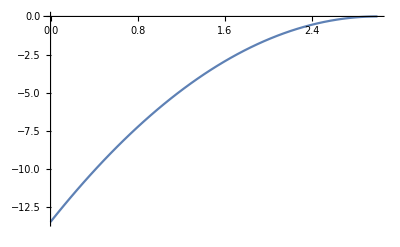

```mathematica
Plot[-1.5 x x+9x-13.5,{x,0,3}]
```

```mathematica
1.5 9
```

13.5

```mathematica
13.5
```

```mathematica
y[x_]=a x^2+b x+c

Solve[{y[0]==-13.5,y[3/2]==-3.375,y[3]==0},{a,b,c}]
```

c+b x+a x^2

{{a→-1.5,b→9.,c→-13.5}}

```mathematica
-3/4.5
```

-0.666667

```mathematica
0.667 4.5+6
```

9.0015

```mathematica
Integrate[(-143.625+11 x)(-9+x)/(3EI),{x,0,6}]+Integrate[(-77.625+77.625/4.5 x)(-3.+(3./4.5) x)/(3 EI),{x,0,4.5}]+Integrate[(-4.6182 x^2 +17.78 x)(3/4.5 x)/(3 EI),{x,0,4.5}]+Integrate[(-1.5 x^2+9 x-13.5)(3-x)/( 3 EI),{x,0,3}]
```

0.359008

```mathematica
e i
```

4218.9

```mathematica
a=(-143.625(2(-9)+(-3))+(-77.625)((-9)+2(-3)))/(3 e i)
b=4.5/3 (-77.625(-3))/(3 e i)
c=-4.5/4 (-13.5 3)/(3 e i)
d=3/4 (-13.5 3)/(3 e i)
a+b+c+d
```

0.330299

0.027599

0.00359987

-0.00239991

0.359098

```mathematica
a=(143.625(2 9+3)+77.625(9+2 3))/(3 e i)
b=4.5/3 (77.625 3)/(3 e i)
c=4.5/4 (13.5 3)/(3 e i)
d=3/4 (13.5 3)/(3 e i)
a+b+c+d
```

0.330299

0.027599

0.00359987

0.00239991

0.363898

```mathematica
Integrate[-qq x^2 /2 +qq L x- qq L^2 /2,x,x]/.x->L
```

-(L^4 qq)/8

```mathematica
Integrate[-qq x^2 /2 +qq L x- qq L^2 /2,x]
```

-1/2 L^2 qq x+1/2 L qq x^2-(qq x^3)/6

```mathematica
-2Integrate[(-4 x^2 /2 + 8 x)(x/4),{x,0,4}]/(Integrate[(-x/4)(-x/4),{x,0,4}]+Integrate[(1-x/4)(1-x/4),{x,0,4}])
```

-8

```mathematica
Integrate[(1-x/4)(1-x/4),{x,0,4}]
```

4/3

```mathematica
4^3/48
```

4/3

```mathematica
Integrate[(-x/4)(-x/4),{x,0,4}]
```

4/3

```mathematica
-2Integrate[(-4 x^2 /2 + 8 x)(x/4),{x,0,4}]
```

-64/3

```mathematica
9 64
```

576

```mathematica
(3 64)/(8 3)
```

8

```mathematica
-2Integrate[(-4 x^2 /2 + 8 x)(x/4),{x,0,4}]
```

```mathematica
2 (-4 4^4/32 + 8 4^3/12)
```

64/3

```mathematica
68/48.
```

1.41667

```mathematica
4+1.41
```

5.41

```mathematica
-Integrate[(- 4 x^2 /2 + 16 x/2)(-1 +x/4.),{x,0,4}]/(Integrate[(-1 +x/4)(-1 +x/4),{x,0,4}]+Integrate[(-1)(-1),{x,0,4}])
```

2.

```mathematica
-4^4 /8 + 4 4^3/3 - 8 4^2/2
```

-32/3

```mathematica
-4^4 /8
```

-32

```mathematica
266/8
```

133/4

```mathematica
4 4 4 4
```

256

```mathematica
4 4^3/3
```

256/3

```mathematica
(-1)(-1)
```

1

```mathematica
(-1)^2
```

1

```mathematica
-Integrate[(- 4 x^2 /2 + 16 x/2)(-1 +x/4),{x,0,4}]
```

32/3

```mathematica
-256/8 + 256/3 - 128/2
```

-32/3

```mathematica
(Integrate[(-1 +x/4)(-1 +x/4),{x,0,4}]+Integrate[(-1)(-1),{x,0,4}])
```

16/3

```mathematica
16/3.
```

5.33333

```mathematica
Table[Fibonacci[n],{n,20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
(Integrate[(-1 +x/4)(-1 +x/4),{x,0,4}]+Integrate[(-1)(-1),{x,0,4}])
```

```mathematica
Solve[{VA+VD-34==0,HA+HD==0,-3 VA+ 4 HA+10 1.5==0,VD 6+HD 4-24 4==0},{HA,HD,VA,VD}]
Solve[{VA+VD-34==0,HA+HD==0,-3 VA+ 4 HA+10 1.5==0,VD 6+HD 4-24 4==0},{HA,HD,VA,VD}]
```

{{HA→6.5,HD→-6.5,VA→13.6667,VD→20.3333}}

{{HA→6.5,HD→-6.5,VA→13.6667,VD→20.3333}}

```mathematica
6 5/4.
```

7.5

```mathematica
6.5
```

6.5

```mathematica
4 4
```

```mathematica
34 0.75
```

25.5

```mathematica
42.75/3.
```

14.25

```mathematica
18+3.75
```

21.75

```mathematica
21.75+25.5
```

```mathematica
47.25/2.25
```

21.

```mathematica
/3.
```

```mathematica
Solve[{VA+VD-34==0,HA+HD==0,-3 VA+ 4 HA+10 1.5==0,VD 6+HD 4-24 3==0},{HA,HD,VA,VD}]
```

{{HA→8.5,HD→-8.5,VA→16.3333,VD→17.6667}}

```mathematica
14.25+25.5
```

39.75

```mathematica
39.75/2.25
```

17.6667

```mathematica
8.5 4
```

34.

```mathematica
Inverse[{{4.75,-12.75},{-12.75,69}}].{110.67,-415.15}
Inverse[{{4.75,-12.75},{-12.75,69}}].{120.09,-473.3}
```

{14.1843,-3.39566}

{13.6308,-4.34069}

18.3515

```mathematica
2.5/6 (26.28(2 0.77+0.55)+17.24(0.77+2 0.55))+5 5/12 26.68 1+2.5/6 17.34(1+2 0.77)
```

110.253

```mathematica
2.5 1/3 17.34 1.5+5 2/3 3 26.68+2.5/6(3 (2 26.68+17.3)+1.5( 26.68+2 17.3))
```

415.1

```mathematica
5/3 (1 1+1 0.55+0.55^2)+5/3 1.
```

4.75417

```mathematica
5 3(1+2 0.55)/6 + 5 1 3/2.
```

12.75

```mathematica
5/3 3 3 + 5 3 3+
```

60

1.66667

```mathematica
5 2/3 3 26.68
```

266.8

55.5833

```mathematica
2.5/6(3 (2 26.68+17.3)+1.5( 26.68+2 17.3))
```

126.625

12.75

```mathematica
5 1 3/2.
```

7.5

```mathematica
26.67-17.33
```

9.34

```mathematica
9.34/2.5
```

3.736

```mathematica
Integrate[(3.736 x+17.35)(1.5+1.5/2.5 x),{x,0,2.5}]
```

126.781

```mathematica
0.77-1
```

-0.23

```mathematica
0.23/2.5
```

0.092

```mathematica
Integrate[(1-0.092 x)(17.34/2.5 x),{x,0,2.5}]
```

18.3515

```mathematica
Integrate[(17.35+(26.68-17.35)/2.5 x)(0.77-(0.77-0.55)/2.5 x),{x,0,2.5}]
```

35.8971

```mathematica
Clear[a,b,c]
```

c+b x+a x^2

{{a→-2.0024,b→4.676,c→26.68}}

26.68+4.676 x-2.0024 x^2

```mathematica
Integrate[f 3,{x,0,5}]
```

325.25

```mathematica
325.25+21.67+126.68
```

473.6

```mathematica
Integrate[f (-1+x/5),{x,0,5}]
```

-65.325

```mathematica
65+36.74+18.35
```

120.09

```mathematica
Integrate[(17.34/2.5 x)(1.5/2.5 x),{x,0,2.5}]
```

21.675

{12.65,-4.70606}

```mathematica
Integrate[(3/5 x)(-1+(1-0.55)/5 x),{x,0,5}]
```

-5.25

```mathematica
y[x_]=a x^2+b x+c

sol=Solve[{y[0]==26.68,y[5]==0,y[2.5]==25.855},{a,b,c}]
f=y[x]/.sol[[1]]
```

c+b x+a x^2

{{a→-2.0024,b→4.676,c→26.68}}

26.68+4.676 x-2.0024 x^2

```mathematica
d11=Integrate[(-1 +(1-0.55)/5 x)^2,{x,0,5}]+Integrate[(-0.55+0.55/5 x)^2,{x,0,5}]
d12=Integrate[(3/5 x)(-1+(1-0.55)/5 x),{x,0,5}]+Integrate[(-0.55+0.55/5 x)(3),{x,0,5}]
d22=Integrate[(3/5x)^2,{x,0,5}]+Integrate[(3)^2,{x,0,5}]+Integrate[(3- x)^2,{x,0,3}]
d10=Integrate[(-1+(1-0.775)/2.5  x)(17.34/2.5 x),{x,0,2.5}]+Integrate[(17.35+(26.68-17.35)/2.5 x)(-0.775+(0.775-0.55)/2.5 x),{x,0,2.5}]+Integrate[f (-0.55+x 0.55/5),{x,0,5}]
d20=Integrate[(17.33/2.5 x)(1.5/2.5 x),{x,0,2.5}]+Integrate[(17.33+(26.67-17.33)/2.5 x)(1.5+1.5/2.5 x),{x,0,2.5}]+Integrate[f 3,{x,0,5}]
Inverse[{{d11,d12},{d12,d22}}].{-d10,-d20}
```

3.59167

-9.375

69

-90.3775

473.581

{11.231,-5.33755}